```mathematica
x^2+y^2+z^2==1
```

x^2+y^2+z^2==1

```mathematica
ContourPlot3D[x^2+y^2+z^2==1,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
Manipulate[
ContourPlot3D[x^2+y^2+z^2==1,{x,-1,1},{y,-1,1},{z,-1,1}]
,{a, 1, 5}]
```

```mathematica
Manipulate[
ContourPlot3D[x^2+y^2+z^2==a,{x,-1,1},{y,-1,1},{z,-1,1}]
,{a, 1, 5}]
```

```mathematica
Manipulate[
ContourPlot3D[x^2+y^2+z^2==a,{x,-1,1},{y,-1,1},{z,-1,1}]
,{a, .01, 5}]
```

```mathematica
D[L[x,f[x],f'[x]],f'[x]]-D[D[L[x,f[x],f'[x]]],f[x],x]==0
```

L^(0,0,1)[x,f[x],f'[x]]-f''[x] L^(0,1,1)[x,f[x],f'[x]]-f'[x] L^(0,2,0)[x,f[x],f'[x]]-L^(1,1,0)[x,f[x],f'[x]]==0

```mathematica
DSolve[%6,{f[x],f[x],L[x,f[x],f'[x]],L[x,f[x],f'[x]],L[x,f[x],f'[x]],L[x,f[x],f'[x]]},{x}]
```

DSolve::ivar2: The independent variable x should not appear in two different arguments of the dependent variable L[x,f[x],f'[x]].

DSolve[L^(0,0,1)[x,f[x],f'[x]]-f''[x] L^(0,1,1)[x,f[x],f'[x]]-f'[x] L^(0,2,0)[x,f[x],f'[x]]-L^(1,1,0)[x,f[x],f'[x]]==0,{f[x],f[x],L[x,f[x],f'[x]],L[x,f[x],f'[x]],L[x,f[x],f'[x]],L[x,f[x],f'[x]]},{x}]

```mathematica
DSolve[
{Derivative[0,0,1][L][x,f[x],f'[x]]-f''[x] Derivative[0,1,1][L][x,f[x],f'[x]]-f'[x] Derivative[0,2,0][L][x,f[x],f'[x]]-Derivative[1,1,0][L][x,f[x],f'[x]]==0},f[x],x]
```

DSolve[{L^(0,0,1)[x,f[x],f'[x]]-f''[x] L^(0,1,1)[x,f[x],f'[x]]-f'[x] L^(0,2,0)[x,f[x],f'[x]]-L^(1,1,0)[x,f[x],f'[x]]==0},f[x],x]

```mathematica
Element[x, Reals]
```

x∈ℝ

```mathematica
Element[x, Reals]∧Element[x, Primes]
```

x∈ℝ&&x∈Primes

```mathematica
Reduce[x∈Reals&&x∈Primes]
```

x∈Primes&&x≥2

```mathematica
FindInstance[x∈Primes&&x≥2,{x}]
```

{{x→2}}

```mathematica
FindInstance[x∈Primes&&x≥2,{x}, Reals, 10]
```

{{x→4787},{x→463},{x→6991},{x→2},{x→3847},{x→4733},{x→3823},{x→5857},{x→6277},{x→4967}}

```mathematica
D[√(1+f'[x]^2),f[x]]-D[D[√(1+f'[x]^2),x],f'[x]]==0
```

(f'[x]^2 f''[x])/((1+f'[x]^2)^(3/2))-f''[x]/(√(1+f'[x]^2))==0

```mathematica
DSolve[(f'[x]^2 f''[x])/((1+f'[x]^2)^(3/2))-f''[x]/(√(1+f'[x]^2))==0,{f[x],f[x]},{x}]
```

{{f[x]→C[1]+x C[2]}}

```mathematica
VariationalD
```

VariationalD

```mathematica
$System
```

Linux x86 (64-bit)

```mathematica
Area[Disk[]]
```

π

```mathematica
Area[Sphere[]]
```

4 π

```mathematica
Area[{r Sin[θ],r Cos[θ]},{r,1,2},{θ,0,2Pi}]
```

3 π

```mathematica
ContourPlot3D[x^2+y^2+z^2==0, {x,y,z}∈Cuboid[]]
```

ContourPlot3D::pllim: Range specification {x,y,z}∈Cuboid[] is not of the form {x, xmin, xmax}.

ContourPlot3D[x^2+y^2+z^2==0,{x,y,z}∈Cuboid[]]

```mathematica
ContourPlot3D[x^2+y^2+z^2==0, {x,y,z}∈Sphere[]]
```

ContourPlot3D::idomdim: {x,y,z}∈Sphere[] does not have a valid dimension as a plotting domain.

ContourPlot3D[x^2+y^2+z^2==0,{x,y,z}∈Sphere[]]

```mathematica
ContourPlot3D[x^2+y^2==1,{x,-1,1},{y,-1,1}]
```

ContourPlot3D::argrx: ContourPlot3D called with 3 arguments; 4 arguments are expected.

ContourPlot3D[x^2+y^2==1,{x,-1,1},{y,-1,1}]

```mathematica
ContourPlot3D[x^2+y^2==1,{x,-1,1},{y,-1,1}, {z, -1,1}]
```

-Graphics3D-

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
VariationalMethods`VariationalD[√(1+D[f[x,y,z],y]^2+D[f[x,y,z],z]^2),f[x,y,z],{x,y,z}]
```

(-f^(0,0,2)[x,y,z] (1+(f^(0,1,0)[x,y,z])^2)+2 f^(0,0,1)[x,y,z] f^(0,1,0)[x,y,z] f^(0,1,1)[x,y,z]-f^(0,2,0)[x,y,z]-(f^(0,0,1)[x,y,z])^2 f^(0,2,0)[x,y,z])/((1+(f^(0,0,1)[x,y,z])^2+(f^(0,1,0)[x,y,z])^2)^(3/2))

```mathematica
VariationalMethods`EulerEquations[√(1+D[f[x,y,z],y]^2+D[f[x,y,z],z]^2),f[x,y,z],{x,y,z}]
```

(-f^(0,0,2)[x,y,z] (1+(f^(0,1,0)[x,y,z])^2)+2 f^(0,0,1)[x,y,z] f^(0,1,0)[x,y,z] f^(0,1,1)[x,y,z]-f^(0,2,0)[x,y,z]-(f^(0,0,1)[x,y,z])^2 f^(0,2,0)[x,y,z])/((1+(f^(0,0,1)[x,y,z])^2+(f^(0,1,0)[x,y,z])^2)^(3/2))==0

```mathematica
DSolve[%27,{f[x,y,z],f[x,y,z],f[x,y,z],f[x,y,z],f[x,y,z]},{x,y,z}]
```

DSolve[(-f^(0,0,2)[x,y,z] (1+(f^(0,1,0)[x,y,z])^2)+2 f^(0,0,1)[x,y,z] f^(0,1,0)[x,y,z] f^(0,1,1)[x,y,z]-f^(0,2,0)[x,y,z]-(f^(0,0,1)[x,y,z])^2 f^(0,2,0)[x,y,z])/((1+(f^(0,0,1)[x,y,z])^2+(f^(0,1,0)[x,y,z])^2)^(3/2))==0,{f[x,y,z],f[x,y,z],f[x,y,z],f[x,y,z],f[x,y,z]},{x,y,z}]

```mathematica
VariationalMethods`EulerEquations[√(1+f'[x]^2),f[x],{x}]
```

-f''[x]/((1+f'[x]^2)^(3/2))==0

```mathematica
DSolve[-f''[x]/((1+f'[x]^2)^(3/2))==0,{f[x],f[x]},{x}]
```

{{f[x]→C[1]+x C[2]}}

```mathematica
VariationalMethods`EulerEquations[f[x] √(1+f'[x]^2),f[x],{x}]
```

(1+f'[x]^2-f[x] f''[x])/((1+f'[x]^2)^(3/2))==0

```mathematica
DSolve[(1+f'[x]^2-f[x] f''[x])/((1+f'[x]^2)^(3/2))==0,{f[x],f[x]},{x}]
```

{{f[x]→-(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))},{f[x]→(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))}}

```mathematica
(ⅇ^-1 Tanh[ⅇ^1 (x+1)])/(√(-1+Tanh[ⅇ^1 (x+1)]^2))
```

Tanh[ⅇ (1+x)]/(ⅇ √(-1+Tanh[ⅇ (1+x)]^2))

```mathematica
Tanh[ⅇ (1+x)]/(ⅇ √(-Sech[ⅇ (1+x)]^2))
```

```mathematica
Simplify[Tanh[ⅇ (1+x)]/(ⅇ √(-1+Tanh[ⅇ (1+x)]^2))]
```

Tanh[ⅇ (1+x)]/(ⅇ √(-Sech[ⅇ (1+x)]^2))

```mathematica
Plot[Tanh[ⅇ (1+x)]/(ⅇ √(-Sech[ⅇ (1+x)]^2)), {x, -3, 3}]
```

-Graphics-

```mathematica
VariationalMethods`EulerEquations[Abs[f[x]] √(1+f'[x]^2),f[x],{x}]
```

(Abs'[f[x]] (1+f'[x]^2)-Abs[f[x]] f''[x])/((1+f'[x]^2)^(3/2))==0

```mathematica
DSolve[(Abs'[f[x]] (1+f'[x]^2)-Abs[f[x]] f''[x])/((1+f'[x]^2)^(3/2))==0,{Abs[f[x]],f[x],f[x]},{x}]
```

DSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in Abs[f[x]] should literally match the independent variables.

DSolve[(Abs'[f[x]] (1+f'[x]^2)-Abs[f[x]] f''[x])/((1+f'[x]^2)^(3/2))==0,{Abs[f[x]],f[x],f[x]},{x}]

```mathematica
DSolve[(Abs'[f[x]] (1+f'[x]^2)-Abs[f[x]] f''[x])/((1+f'[x]^2)^(3/2))==0,f[x],x]
```

{{f[x]→InverseFunction[-1/(√(-1+ⅇ^(2 C[1]) Abs[K[1]]^2))K[1]1#1&][x+C[2]]},{f[x]→InverseFunction[1/(√(-1+ⅇ^(2 C[1]) Abs[K[2]]^2))K[2]1#1&][x+C[2]]}}

```mathematica
D[U[x,t],t]==α D[U[x,t],x]
```

U^(0,1)[x,t]==α U^(1,0)[x,t]

```mathematica
DSolve[Derivative[0,1][U][x,t]==α Derivative[1,0][U][x,t],{U[x,t],U[x,t]},{t,x}]
```

{{U[x,t]→C[1][x+t α]}}

```mathematica
D[U[x,t],t]==D[U[x,t],x]
```

U^(0,1)[x,t]==U^(1,0)[x,t]

```mathematica
DSolve[Derivative[0,1][U][x,t]==Derivative[1,0][U][x,t],{U[x,t],U[x,t]},{t,x}]
```

{{U[x,t]→C[1][t+x]}}

```mathematica
Laplacian[f[x],{x}]==λ f[x]
```

f''[x]==λ f[x]

```mathematica
DSolve[f''[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x √λ) C[1]+ⅇ^(-x √λ) C[2]}}

```mathematica
ⅇ^(x √2)+ⅇ^(-x √2)
```

ⅇ^(-√2 x)+ⅇ^(√2 x)

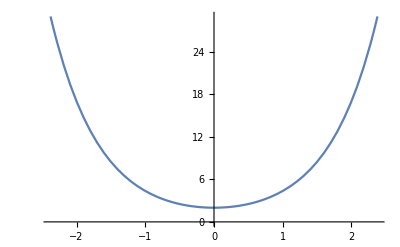

```mathematica
Plot[ⅇ^(-√2 x)+ⅇ^(√2 x),{x,-2.379098806717563,2.379098806717563}]
```

```mathematica
ⅇ^(-√x)+ⅇ^(√x)
```

ⅇ^(-√x)+ⅇ^(√x)

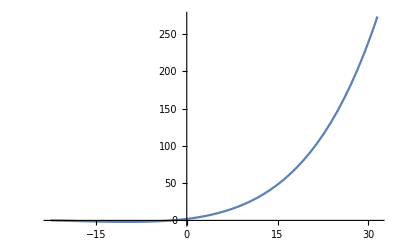

```mathematica
Plot[ⅇ^(-√x)+ⅇ^(√x),{x,-22.5,31.5}]
```

```mathematica
norm[x_Reals]:=ⅇ^(-√2 x)+ⅇ^(√2 x)
```

```mathematica
norm[0]
```

norm[0]

```mathematica
norm[x_]:=ⅇ^(-√2 x)+ⅇ^(√2 x)
```

```mathematica
norm[4]
```

ⅇ^(-4 √2)+ⅇ^(4 √2)

```mathematica
norm[0]
```

2

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
ⅇ^(-x^2/2)
```

ⅇ^(-x^2/2)

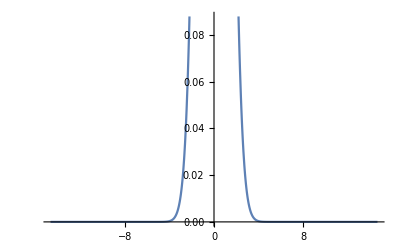

```mathematica
Plot[ⅇ^(-x^2/2),{x,-14.696938456699069,14.696938456699069}]
```

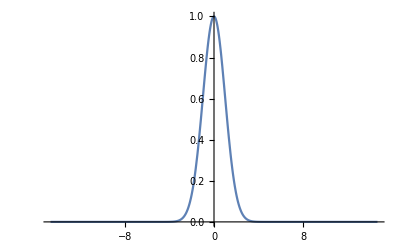

```mathematica
Plot[ⅇ^(-x^2/2),{x,-14.696938456699069,14.696938456699069}, PlotRange->{0,1}]
```

```mathematica
expr[x_]:=ⅇ^(-x^2/2)
```

```mathematica
matrix[x_]:=Sin[1/x]
```

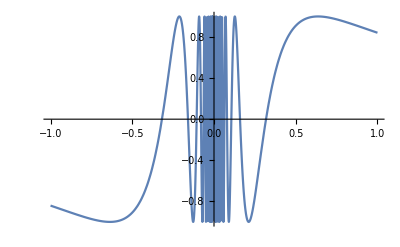

```mathematica
Plot[matrix[x], {x, -1, 1}]
```

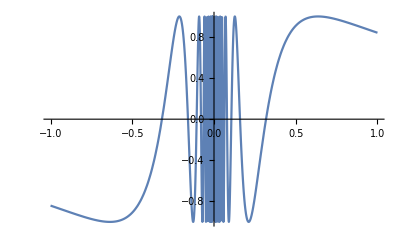

```mathematica
Plot[matrix[x], {x, -1, 1}, PlotRange->{-1,1}, PlotLegends->"Expressions"]
```

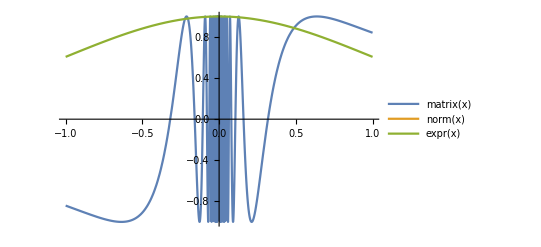

```mathematica
Plot[
{matrix[x], norm[x], expr[x]},
{x, -1, 1},
PlotRange->{-1,1},
PlotLegends->"Expressions"]
```

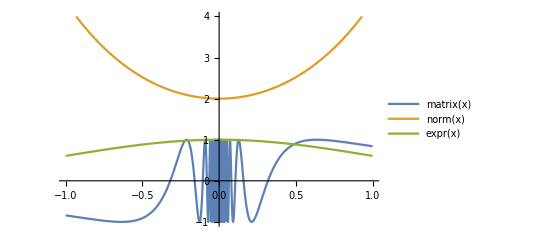

```mathematica
Plot[
{matrix[x], norm[x], expr[x]},
{x, -1, 1},
PlotRange->{-1,4},
PlotLegends->"Expressions"]
```

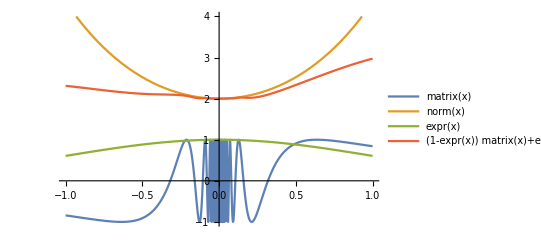

```mathematica
Plot[
{matrix[x], norm[x], expr[x],((1-expr[x])matrix[x])+((expr[x])norm[x])},
{x, -1, 1},
PlotRange->{-1,4},
PlotLegends->"Expressions"]
```

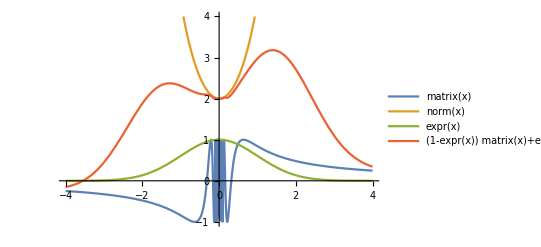

```mathematica
Plot[
{matrix[x], norm[x], expr[x],((1-expr[x])matrix[x])+((expr[x])norm[x])},
{x, -4, 4},
PlotRange->{-1,4},
PlotLegends->"Expressions"]
```

```mathematica
Plot[{
matrix[x],
norm[x],
expr[x],
((1-expr[x])matrix[x])+((expr[x])norm[x])
},{x, -4, 4},
PlotRange->{-1,4},
PlotLegends->"Expressions"]
```

-Graphics-

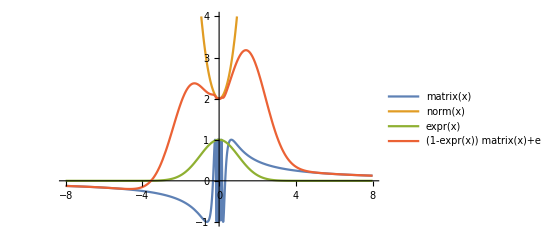

```mathematica
Plot[{
matrix[x],
norm[x],
expr[x],
((1-expr[x])matrix[x])+((expr[x])norm[x])
},{x, -8, 8},
PlotRange->{-1,4},
PlotLegends->"Expressions"]
```

```mathematica
CloudPut[Plot[{
matrix[x],
norm[x],
expr[x],
((1-expr[x])matrix[x])+((expr[x])norm[x])
},{x, -8, 8},
PlotRange->{-1,4},
PlotLegends->"Expressions"]]
```

CloudObject[https://www.wolframcloud.com/objects/0473dd05-25d0-4da6-8421-526ad3c332c0]

```mathematica
Integrate[f[x] g[x],x]
```

∫f[x] g[x]ⅆx

```mathematica
Integrate[f[g[x]] ,x]
```

∫f[g[x]]ⅆx

```mathematica
VariationalMethods`VariationalD[√((1+f'[x]^2)/(2g(h-y))), f[x],x]
```

-(√((1+f'[x]^2)/(2 g h-2 g y)) f''[x])/((1+f'[x]^2)^2)

```mathematica
VariationalMethods`EulerEquations[√((1+f'[x]^2)/(2g(h-y))), f[x],x]
```

-(√((1+f'[x]^2)/(2 g h-2 g y)) f''[x])/((1+f'[x]^2)^2)==0

```mathematica
DSolve[-(√((1+f'[x]^2)/(2 g h-2 g y)) f''[x])/((1+f'[x]^2)^2)==0,{f[x],f[x]},{x,y}]
```

DSolve::alliv: The function f[x] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

DSolve[-(√((1+f'[x]^2)/(2 g h-2 g y)) f''[x])/((1+f'[x]^2)^2)==0,{f[x],f[x]},{x,y}]

```mathematica
DSolve[-(√((1+f'[x]^2)/(2 g h-2 g y)) f''[x])/((1+f'[x]^2)^2)==0,{f[x]},{x}]
```

{{f[x]→-ⅈ x+C[1]},{f[x]→ⅈ x+C[1]},{f[x]→C[1]+x C[2]}}

```mathematica
-x^2
```

-x^2

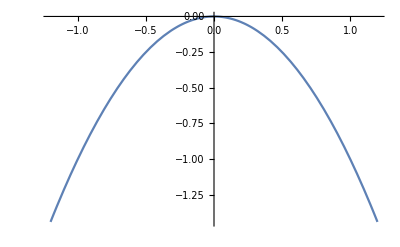

```mathematica
Plot[-x^2,{x,-1.2,1.2}]
```

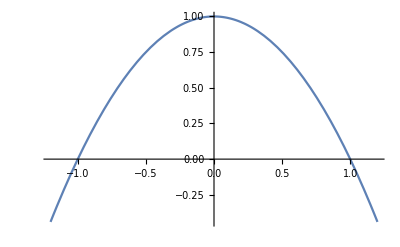

```mathematica
Plot[1-x^2,{x,-1.2,1.2}]
```

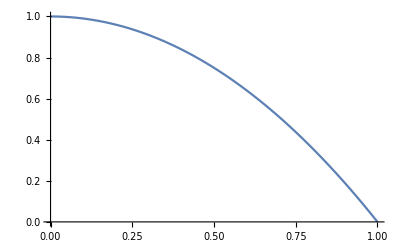

```mathematica
Plot[1-x^2,{x,0,1}]
```

```mathematica
g f[x]
```

g f[x]

```mathematica
{0,g (1-x^2)}->1/2{1,2x}^2
```

{0,g (1-x^2)}→{1/2,2 x^2}

```mathematica
{g (1-x^2),(2 x^2)/(1/2)}
```

{g (1-x^2),4 x^2}

```mathematica
Differences@{g (1-x^2),4 x^2}
```

{4 x^2-g (1-x^2)}

```mathematica
g (1-x^2)-4 x^2
```

-4 x^2+g (1-x^2)

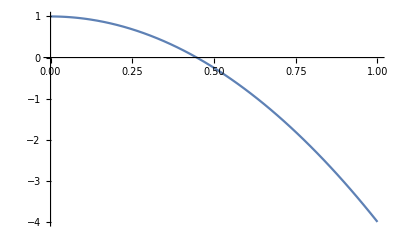

```mathematica
Plot[-4 x^2+ (1-x^2),{x,0,1}]
```

```mathematica
Integrate[g (1-x^2)-4 x^2,{x,0,1}]
```

-4/3+(2 g)/3

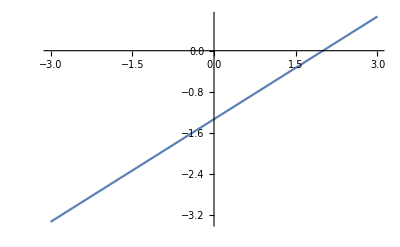

```mathematica
Plot[-4/3+(2 g)/3,{g,-3.,3.}]
```

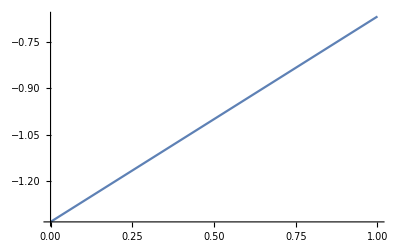

```mathematica
Plot[-4/3+(2 g)/3,{g,0,1}]
```

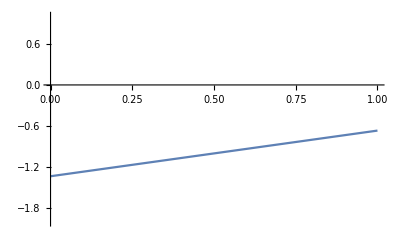

```mathematica
Plot[-4/3+(2 g)/3,{g,0,1}, PlotRange->{-2,1}]
```

```mathematica
Plot[-4/3+(2 g)/3,{g,0,1}, PlotRange->{-2,1}]
```